```mathematica
RootPath="/Users/cdschillaci/Desktop/Paper with Tom/Mathematica";
StringJoin[RootPath,"/SciDraw-0.0.5/packages"];
AppendTo[$Path,%];
Get["SciDraw`"]
```

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.5 (October 11, 2014)
View color paletteVisit home page  -Graphics-

```mathematica
(* Options for all plots *)
TexWidthPoints=468;
MarginSizeInches=0.6;
CanvasWidth=TexWidthPoints/72.0-2*MarginSizeInches;
CanvasHeight=CanvasWidth/GoldenRatio;
TextPoint=10;
GridLineColor=LightGray;
```

```mathematica
(* Options for energy spectrum plots *)
EGSColor=Firebrick;
ExcitationColor=Firebrick;

SpectraXPanelGap={.1};
SpectraYPanelSizes={1,.5/GoldenRatio}
SpectraYPanelGap={.015};

SpectraYFrameLabel={Row[{"E-",Subscript["E","GS"]}],Subscript["E","GS"]};
```

```mathematica
(* Run Weyl in Busch Basis for a=-1, a=∞ first *)
αMaxW=0.5;
nEnergiesWeyl=20;
WEnergiesm1=Import["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWm1.m"];
WExcitationsm1=Import["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWm1Excitation.m"];
WEnergiesInf=Import["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWInf.m"];
WExcitationsInf=Import["/Users/cdschillaci/Desktop/Paper\ with\ Tom/Mathematica/Saved/aWInfExcitation.m"];
```

```mathematica
(* This function removes jumps resulting from miscalculation of eigenvalue degeneracies *)
Clean[Data_]:=Module[{nEigValues,i,j,temp},
temp=Data;
nEigValues=Dimensions[Data][[1]];
For[i=2,i≤nEigValues,i++,
temp[[i]]=Sort[temp[[i]]];
For[j=5,j≥1,j--,
If[Abs[temp[[i]][[j,2]]-temp[[i]][[j+1,2]]]>.1,
temp[[i]]=Delete[temp[[i]],j];
](* End if *)
](* End j loop *)
] ;(* End i loop *)
Return[temp];
]
WEnergiesm1=Clean[WEnergiesm1];
WExcitationsm1=Clean[WExcitationsm1];
WEnergiesInf=Clean[WEnergiesInf];
WExcitationsInf=Clean[WExcitationsInf];
```

```mathematica
WeylFig=Figure[
Multipanel[
{ (*plots*)
FigurePanel[
(* Excitation Energies *)
{
Table[FigRule[Horizontal,2+i/2,All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,5}];
Table[FigRule[Vertical,0.1+0.1*i,All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,3}];
FigGraphics[ListPlot[Table[WExcitationsm1[[i]],{i,1,nEnergiesWeyl-1,1}],Joined->True,PlotStyle->ExcitationColor]];
},
{1,1}
];
FigurePanel[
(* GS Energy *)
{
FigRule[Horizontal,1.5,All,LineDashing->Dashed,LineColor->GridLineColor];
Table[FigRule[Vertical,0.1+0.1*i,All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,3}];
FigGraphics[ListPlot[WEnergiesm1[[1]],Joined->True,PlotStyle->EGSColor]];
},
{2,1}
] ;
FigurePanel[
(* Excitation Energies *)
{
Table[FigRule[Horizontal,2+i/2,All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,5}];
Table[FigRule[Vertical,0.1+0.1*i,All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,3}];
FigGraphics[ListPlot[Table[WExcitationsInf[[i]],{i,1,nEnergiesWeyl-1,1}],Joined->True,PlotStyle->ExcitationColor]];
},
{1,2}
];
FigurePanel[
(* GS Energy *)
{
FigRule[Horizontal,1.5,All,LineDashing->Dashed,LineColor->GridLineColor];
Table[FigRule[Vertical,0.1+0.1*i,All,LineDashing->Dashed,LineColor->LightGray],{i,0,3}];
FigGraphics[ListPlot[WEnergiesInf[[1]],Joined->True,PlotStyle->EGSColor]];
},
{2,2}
] ;
},
(* geometry *)
Dimensions->{2,2},
XPanelGaps->SpectraXPanelGap,
YPanelSizes->SpectraYPanelSizes,
YPanelGaps->SpectraYPanelGap,
(* axes *)
XPlotRange->{0,αMaxW},
XFrameLabel->Subscript["α","W"],

YPlotRange->{{{1.4,4.4},{1.4,4.4}},{{.25,2.75},{.25,2.75}}},
YFrameLabel->SpectraYFramLabel,
YTicks->{LinTicks[0.5,4.5,0.5,5],LinTicks[-0.5,2.5,1,5]},

(* Labels and Font Formatting *)
PanelLetter->None,
FontSize->TextPoint
]
,CanvasSize->{CanvasWidth,CanvasHeight},CanvasMargin->MarginSizeInches]
```

-Graphics-

```mathematica
Export [StringJoin[RootPath,"/NiceFigures/WeylSpectrum.eps"],WeylFig]
```

```mathematica
a=1;
α=0.5;
Get[StringJoin[RootPath,"/Saved/aW",ToString[a],"Convergence_alpha=",ToString[α],".m"]]
For[i=1,i≤8,i++,ConvergenceW1[i]=Convergence[i]]
a=-1;
Get[StringJoin[RootPath,"/Saved/aW",ToString[a],"Convergence_alpha=",ToString[α],".m"]]
For[i=1,i≤8,i++,ConvergenceWm1[i]=Convergence[i]]
Clear[Convergence]
```

```mathematica
WeylConvFig=Figure[
Multipanel[
{ (*plots*)
FigurePanel[
(* a=-1 *)
{
Table[FigRule[Horizontal,1+i,All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,3}];
Table[FigRule[Vertical,10(1+i),All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,4}];
FigGraphics[ListPlot[Table[ConvergenceWm1[i],{i,1,8}],Joined->True]];
},
{1,1}
];
FigurePanel[
(* a=-1 *)
{
Table[FigRule[Horizontal,-1+i,All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,5}];
Table[FigRule[Vertical,10(1+i),All,LineDashing->Dashed,LineColor->GridLineColor],{i,0,4}];
FigGraphics[ListPlot[Table[ConvergenceW1[i],{i,1,8}],Joined->True]];
},
{1,2}
];
}
(* geometry *),
Dimensions->{1,2},
(* axes *)
XPlotRange->{6,50},
XFrameLabel->Subscript["E","max"],
XPanelGaps->{.1},

YPlotRange->{{{0.5,5.5},{-1.5,5.5}}},
YFrameLabel->"E",
YShowTickLabels->True,
YTicks->LinTicks[-1.0,5.5],

PanelLetter->None,
FontSize->TextPoint
]
,CanvasSize->{CanvasWidth,CanvasHeight/2},CanvasMargin->MarginSizeInches]
```

-Graphics-

```mathematica
Export [StringJoin[RootPath,"/NiceFigures/WeylConvergence.eps"],WeylConvFig]
```

/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/NiceFigures/WeylConvergence.eps

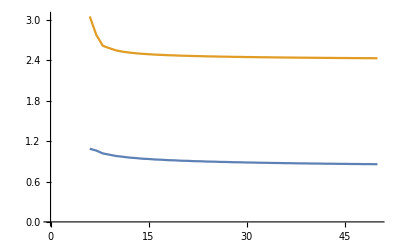

```mathematica
ListPlot[Table[ConvergenceWm1[i],{i,1,2}],Joined->True]
```

```mathematica
FixedPointForm[2.1,2]
```

2.10